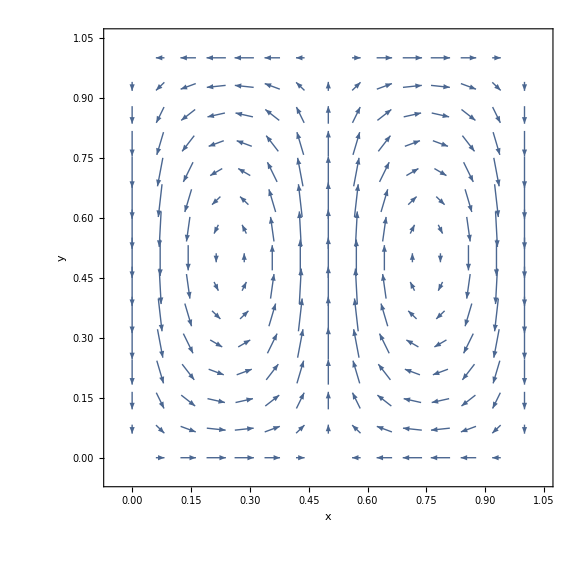

```mathematica
vx[x_,y_] := π*Sin[2*π*x]*Cos[π*y]
vy[x_,y_] := -2*π*Cos[2*π*x]*Sin[π*y]

VectorPlot[{vx[x,y],vy[x,y]},{x,0,1},{y,0,1},FrameLabel->{{HoldForm[y],None},{HoldForm[x],None}},PlotLabel->None,LabelStyle->{FontFamily->"Verdana",16,GrayLevel[0]},ImageSize->Large]
```